```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/autoindent.wl"];
Autoindent["model/model.wl"];
Autoindent["model/data.wl"];
Autoindent["model/gof-metrics.wl"];
```

```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/model.wl"]
```

Fitting model for CA

>> <|chiSquared→1.23663×10^-6,rmsRelativeError→0.318191,rmsRelativeErrorDeaths→0.22047,rmsRelativeErrorPcr→0.377495,meanRelativeErrorDeaths→-0.0576513,meanRelativeErrorPcr→0.010738,rSquaredDeaths→0.0300003,rSquaredPcr→0.00817335,deathResidual7Day→-0.212395,pcrResidual7Day→46.5326|>

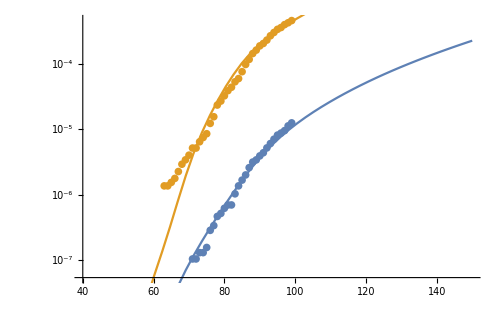
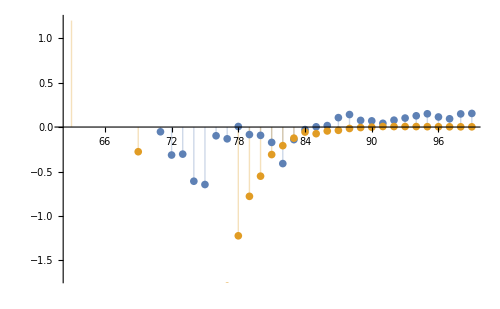
>> Fit for CA
-Graphics--Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 3.31568 | 0.284106 | 11.6706 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[11.6706,62.,HypothesisTesting`TwoSided→True]
ⅇ^importtime | 52.4603 | 1.80198 | 29.1127 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[29.1127,62.,HypothesisTesting`TwoSided→True]
ⅇ^stateAdjustmentForTestingDifferences | 1.31303 | 0.0979278 | 13.4082 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[13.4082,62.,HypothesisTesting`TwoSided→True]
ⅇ^distpow | 1.57759 | 0.449377 | 3.51061 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[3.51061,62.,HypothesisTesting`TwoSided→True] | DF | SS | MS
Model | 4 | 9.90521×10^-10 | 2.4763×10^-10
Error | 62 | 1.51141×10^-11 | 2.43776×10^-13
Uncorrected Total | 66 | 1.00563×10^-9 | 
Corrected Total | 65 | 9.87321×10^-10 |

>> Current Indefinite scenario Generating simulations for CA in the

DatePlus::inc: -1+{icu→<|eventName→icu,day→141.339,thresholdCrossed→0.000177642|>,hospital→<|eventName→hospital,day→150.58,thresholdCrossed→0.000952557|>}[icu][day] is not a recognized calendar increment specification for DatePlus.

DateString::arg: Argument DatePlus[{2020,1,1},-1+{icu→<|eventName→icu,day→141.339,thresholdCrossed→0.000177642|>,hospital→<|eventName→hospital,day→150.58,thresholdCrossed→0.000952557|>}[icu][day]] cannot be interpreted as a date or time input or as a date string format.

DatePlus::inc: -1+{icu→<|eventName→icu,day→141.339,thresholdCrossed→0.000177642|>,hospital→<|eventName→hospital,day→150.58,thresholdCrossed→0.000952557|>}[hospital][day] is not a recognized calendar increment specification for DatePlus.

DateString::arg: Argument DatePlus[{2020,1,1},-1+{icu→<|eventName→icu,day→141.339,thresholdCrossed→0.000177642|>,hospital→<|eventName→hospital,day→150.58,thresholdCrossed→0.000952557|>}[hospital][day]] cannot be interpreted as a date or time input or as a date string format.

DatePlus::inc: -1+{icu→<|eventName→icu,day→141.339,thresholdCrossed→0.000177642|>,hospital→<|eventName→hospital,day→150.58,thresholdCrossed→0.000952557|>}[icu][day] is not a recognized calendar increment specification for DatePlus.

General::stop: Further output of DatePlus::inc will be suppressed during this calculation.

DateString::arg: Argument DatePlus[{2020,1,1},-1+{icu→<|eventName→icu,day→141.339,thresholdCrossed→0.000177642|>,hospital→<|eventName→hospital,day→150.58,thresholdCrossed→0.000952557|>}[icu][day]] cannot be interpreted as a date or time input or as a date string format.

General::stop: Further output of DateString::arg will be suppressed during this calculation.

>> checkpoint

>> Current scenario Generating simulations for CA in the

$Aborted

state | distancingLevel | id | distancingDays | maintain | name | summaryAug1 | totalProjectedDeaths | totalProjectedPCRConfirmed | totalProjectedInfected | totalInfectedFraction | fatalityRate | fatalityRateSymptomatic | fatalityRatePCR | fractionOfSymptomaticHospitalized | fractionOfPCRHospitalized | fractionHospitalizedInICU | fractionOfInfectionsPCRConfirmed | dateContained | dateICUOverCapacity | dateHospitalsOverCapacity | {"r0natural", "importtime", "stateAdjustmentForTestingDifferences"} |  | 
CA | 81/140 | scenario5 | 629 | True | Current Indefinite | <|"totalProjectedDeaths" -> 55414.68915380388, "totalProjectedPCRConfirmed" -> 1.3975058567621086*^6, "totalProjectedInfected" -> 7.45271968052275*^6, "totalInfectedFraction" -> 0.19117946107226982, "fatalityRate" -> 0.007435498922443971, "fatalityRateSymptomatic" -> 0.010622141317777101, "fatalityRatePCR" -> 0.03965256308992835, "fractionOfSymptomaticHospitalized" -> 0.1045692415191976, "fractionOfPCRHospitalized" -> 0.3903580570582791, "fractionHospitalizedInICU" -> 0.12514221060899886, "fractionOfInfectionsPCRConfirmed" -> 0.2678803207168996, "dateContained" -> "Wed 3 Mar 2021 00:00:00", "dateICUOverCapacity" -> DateString[DatePlus[{2020, 1, 1}, -1 + "icu"[[1]]]], "dateHospitalsOverCapacity" -> DateString[DatePlus[{2020, 1, 1}, -1 + "hospital"[[1]]]]|> | 128619. | 3.22554×10^6 | 1.15365×10^7 | 0.295937 | 0.0111489 | 0.015927 | 0.0398751 | 0.106106 | 0.265649 | 0.245761 | 0.399422 | Wed 3 Mar 2021 00:00:00 | DateString[DatePlus[{2020, 1, 1}, -1 + "icu"[[1]]]] | DateString[DatePlus[{2020, 1, 1}, -1 + "hospital"[[1]]]] | 3.31568 | 52.4603 | 1.31303
CA | 81/140 | scenario1 | 90 | True | Current | <|"totalProjectedDeaths" -> 95805.48840951527, "totalProjectedPCRConfirmed" -> 2.334308636742152*^6, "totalProjectedInfected" -> 1.2653803648425965*^7, "totalInfectedFraction" -> 0.3245992692228447, "fatalityRate" -> 0.007571279835801209, "fatalityRateSymptomatic" -> 0.010816114051144585, "fatalityRatePCR" -> 0.041042339860947, "fractionOfSymptomaticHospitalized" -> 0.10510487944910779, "fractionOfPCRHospitalized" -> 0.3988262478554075, "fractionHospitalizedInICU" -> 0.09358012944378664, "fractionOfInfectionsPCRConfirmed" -> 0.2635355120538933, "dateContained" -> "Wed 9 Dec 2020 00:00:00", "dateICUOverCapacity" -> DateString[DatePlus[{2020, 1, 1}, -1 + "icu"[[1]]]], "dateHospitalsOverCapacity" -> DateString[DatePlus[{2020, 1, 1}, -1 + "hospital"[[1]]]]|> | 271017. | 8.30837×10^6 | 2.80324×10^7 | 0.719094 | 0.00966799 | 0.0138114 | 0.0326197 | 0.106106 | 0.250601 | 0.245761 | 0.423407 | Wed 9 Dec 2020 00:00:00 | DateString[DatePlus[{2020, 1, 1}, -1 + "icu"[[1]]]] | DateString[DatePlus[{2020, 1, 1}, -1 + "hospital"[[1]]]] | 3.31568 | 52.4603 | 1.31303
CA | 0.4 | scenario2 | 90 | False | Italy | <|"totalProjectedDeaths" -> 10420.302264504813, "totalProjectedPCRConfirmed" -> 199691.28160573813, "totalProjectedInfected" -> 1.092976549706816*^6, "totalInfectedFraction" -> 0.028037371147028232, "fatalityRate" -> 0.009533875422395836, "fatalityRateSymptomatic" -> 0.013619822031994052, "fatalityRatePCR" -> 0.05218205913004359, "fractionOfSymptomaticHospitalized" -> 0.10476002615753838, "fractionOfPCRHospitalized" -> 0.40137043395839644, "fractionHospitalizedInICU" -> 0.008305053010724353, "fractionOfInfectionsPCRConfirmed" -> 0.26100583723712234, "dateContained" -> "Sat 19 Dec 2020 00:00:00", "dateICUOverCapacity" -> DateString[DatePlus[{2020, 1, 1}, -1 + "icu"[[1]]]], "dateHospitalsOverCapacity" -> DateString[DatePlus[{2020, 1, 1}, -1 + "hospital"[[1]]]]|> | 300061. | 1.33092×10^7 | 2.95266×10^7 | 0.757427 | 0.0101624 | 0.0145177 | 0.0225454 | 0.106106 | 0.164779 | 0.245761 | 0.643931 | Sat 19 Dec 2020 00:00:00 | DateString[DatePlus[{2020, 1, 1}, -1 + "icu"[[1]]]] | DateString[DatePlus[{2020, 1, 1}, -1 + "hospital"[[1]]]] | 3.31568 | 52.4603 | 1.31303
CA | 0.11 | scenario3 | 60 | False | Wuhan | <|"totalProjectedDeaths" -> 1895.098611724348, "totalProjectedPCRConfirmed" -> 50789.792198399766, "totalProjectedInfected" -> 270424.5149119239, "totalInfectedFraction" -> 0.006937012961416695, "fatalityRate" -> 0.007007865438314916, "fatalityRateSymptomatic" -> 0.01001123634044988, "fatalityRatePCR" -> 0.037312588409921806, "fractionOfSymptomaticHospitalized" -> 0.10485526370902226, "fractionOfPCRHospitalized" -> 0.3908030101717432, "fractionHospitalizedInICU" -> 0.0021198749167958258, "fractionOfInfectionsPCRConfirmed" -> 0.26830720588089213, "dateContained" -> "Mon 18 May 2020 00:00:00", "dateICUOverCapacity" -> DateString[DatePlus[{2020, 1, 1}, -1 + "icu"[[1]]]], "dateHospitalsOverCapacity" -> DateString[DatePlus[{2020, 1, 1}, -1 + "hospital"[[1]]]]|> | 249852. | 1.31763×10^7 | 2.9729×10^7 | 0.762616 | 0.00840434 | 0.0120062 | 0.0189622 | 0.106106 | 0.167581 | 0.245761 | 0.633164 | Mon 18 May 2020 00:00:00 | DateString[DatePlus[{2020, 1, 1}, -1 + "icu"[[1]]]] | DateString[DatePlus[{2020, 1, 1}, -1 + "hospital"[[1]]]] | 3.31568 | 52.4603 | 1.31303
CA | 1 | scenario4 | 90 | False | Normal | <|"totalProjectedDeaths" -> 269799.60638692824, "totalProjectedPCRConfirmed" -> 4.729126527364963*^6, "totalProjectedInfected" -> 3.064801282403768*^7, "totalInfectedFraction" -> 0.7861922661533078, "fatalityRate" -> 0.008803168020581108, "fatalityRateSymptomatic" -> 0.01257595431511587, "fatalityRatePCR" -> 0.057050621256534394, "fractionOfSymptomaticHospitalized" -> 0.10618417848329514, "fractionOfPCRHospitalized" -> 0.48170287504983716, "fractionHospitalizedInICU" -> 0.2426231385164922, "fractionOfInfectionsPCRConfirmed" -> 0.22043501084005218, "dateContained" -> "Thu 3 Sep 2020 00:00:00", "dateICUOverCapacity" -> DateString[DatePlus[{2020, 1, 1}, -1 + "icu"[[1]]]], "dateHospitalsOverCapacity" -> DateString[DatePlus[{2020, 1, 1}, -1 + "hospital"[[1]]]]|> | 275052. | 4.7464×10^6 | 3.07208×10^7 | 0.788059 | 0.00895328 | 0.0127904 | 0.0579495 | 0.106106 | 0.480736 | 0.245761 | 0.220716 | Thu 3 Sep 2020 00:00:00 | DateString[DatePlus[{2020, 1, 1}, -1 + "icu"[[1]]]] | DateString[DatePlus[{2020, 1, 1}, -1 + "hospital"[[1]]]] | 3.31568 | 52.4603 | 1.31303

```mathematica
asd=GenerateModelExport[10,{"CA"}];
TableForm[Import["tests/summary.csv"]]
```

```mathematica
sr=integrateModel[
stateDistancingPrecompute["CA"]["scenario1"]["distancingFunction"],
fiducialTestParameterstempParams
]
```

{<|sSq[1]→InterpolatingFunction[…],sSq[2]→InterpolatingFunction[…],sSq[3]→InterpolatingFunction[…],sSq[4]→InterpolatingFunction[…],sSq[5]→InterpolatingFunction[…],sSq[6]→InterpolatingFunction[…],sSq[7]→InterpolatingFunction[…],sSq[8]→InterpolatingFunction[…],sSq[9]→InterpolatingFunction[…],sSq[10]→InterpolatingFunction[…],sSq[11]→InterpolatingFunction[…],sSq[12]→InterpolatingFunction[…],sSq[13]→InterpolatingFunction[…],sSq[14]→InterpolatingFunction[…],sSq[15]→InterpolatingFunction[…],sSq[16]→InterpolatingFunction[…],sSq[17]→InterpolatingFunction[…],sSq[18]→InterpolatingFunction[…],sSq[19]→InterpolatingFunction[…],sSq[20]→InterpolatingFunction[…],Deaq→InterpolatingFunction[…],PCR→InterpolatingFunction[…],RepHq→InterpolatingFunction[…],Eq→InterpolatingFunction[…],EInq→InterpolatingFunction[…],ISq→InterpolatingFunction[…],RSq→InterpolatingFunction[…],IHq→InterpolatingFunction[…],HHq→InterpolatingFunction[…],RHq→InterpolatingFunction[…],ICq→InterpolatingFunction[…],EHq→InterpolatingFunction[…],HCq→InterpolatingFunction[…],CCq→InterpolatingFunction[…],RCq→InterpolatingFunction[…],est→InterpolatingFunction[…],Sq→(∑_s^Cases[outputODE$1604790,sSq[_]] outputSolution$1604790[s][#1]&),Iq→(outputSolution$1604790[ISq][#1]+outputSolution$1604790[IHq][#1]+outputSolution$1604790[ICq][#1]&),Rq→(outputSolution$1604790[RSq][#1]+outputSolution$1604790[RHq][#1]+outputSolution$1604790[RCq][#1]&)|>,<|herd→<|eventName→herd,day→224.284,thresholdCrossed→0.7|>,icu→<|eventName→icu,day→141.339,thresholdCrossed→0.000177642|>,hospital→<|eventName→hospital,day→150.58,thresholdCrossed→0.000952557|>|>}